```mathematica
Quit
```

```mathematica
a[xi_,eta_]:=3xi/(2-Sqrt[3]eta)
b[xi_,eta_]:=(2Sqrt[3]eta-1)/3

i[p_,v_,w_]:=w+(p+1)v-(v(v-1))/2
phi[v_,w_,a_,b_]:=2JacobiP[v,0,0,a]JacobiP[w,2v+1,0,b](1-b)^v/3^(1/4)

p=2;

domain=Triangle[{{-1,-Sqrt[3]/3},{1,-Sqrt[3]/3},{0,2Sqrt[3]/3}}];
centroid=RegionCentroid[domain];

For[c=0,c<(p+1)(p+2)/2,c++,{
Print[vw=Solve[{i[p,v,w]==c,v+w≤p, v≥0, w≥0},{v,w},Integers]],
Print[phi[v,w,a[ξ,η],b[ξ,η]]/.vw],
GraphicsRow[{Plot3D[phi[v,w,a[ξ,η],b[ξ,η]]/.vw, {ξ,-1,1}, {η,-1,1}],
Plot3D[phi[v,w,a[ξ,η],b[ξ,η]]/.vw,{ξ,η}∈domain]},ImageSize->1000]//Print
}]

(*Ntri[p_]:=3*p
Ctrim[p_,m_]:=Binamial[p,m-1]*Ctri
Dvw[v_,w_,f_]:=D[f,{x,w-v+1},{y,v-1}]

phi[v_,w_,a_,b_]:=2JacobiP[v,0,0,a]JacobiP[w,2v+1,0,b](1-b)^v/3^(1/4)
phi2d[i_,xi_,eta_]:=2/3^(1/4)*JacobiP[v,1,1,a]*JacobiP[w,2v+1,0,b]*(1-b[xi_,eta_])^v

phi[v,w,a,b]
phi2d[*)
```

{{v→0,w→0}}

{2/3^(1/4)}

-Graphics-

{{v→0,w→1}}

{2 3^(1/4) η}

-Graphics-

{{v→0,w→2}}

{(2 (3+6 (-1+1/3 (-1+2 √3 η))+5/2 (-1+1/3 (-1+2 √3 η))^2))/3^(1/4)}

-Graphics-

{{v→1,w→0}}

{-(2 3^(3/4) (1+1/3 (1-2 √3 η)) ξ)/(-2+√3 η)}

-Graphics-

{{v→1,w→1}}

{-(3^(3/4) (1+1/3 (1-2 √3 η)) (3+5/3 (-1+2 √3 η)) ξ)/(-2+√3 η)}

-Graphics-

{{v→2,w→0}}

{((1+1/3 (1-2 √3 η))^2 (-4+4 √3 η-3 η^2+27 ξ^2))/(3^(1/4) (-2+√3 η)^2)}

-Graphics-

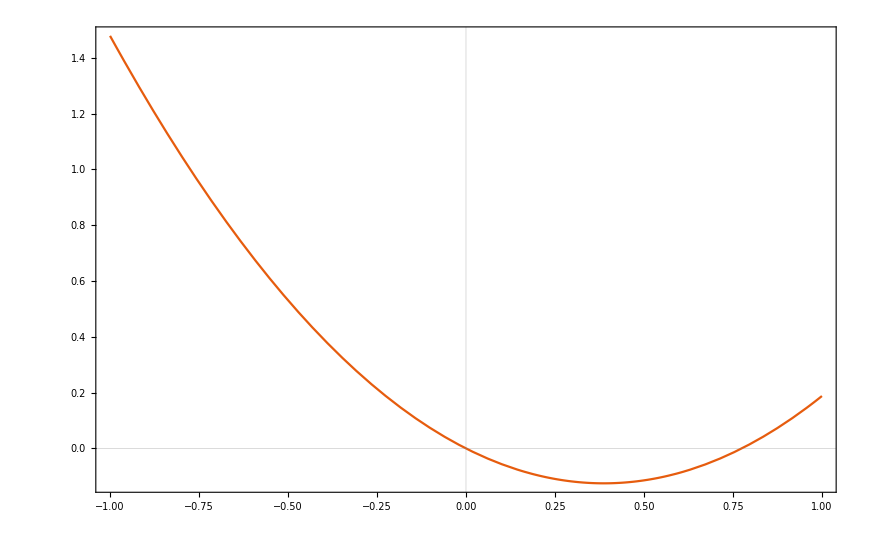

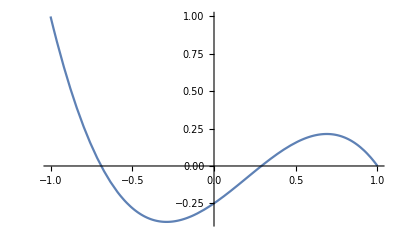

```mathematica
n=3;
points={x,0}/.Solve[LegendreP[n,x]==0,x];
points[[2,2]]=1;

RadauP[n_,x_]:=(-1)^n*0.5*(LegendreP[n,x]-LegendreP[n-1,x])
leg=InterpolatingPolynomial[points,y];
Plot[leg,{y,-1,1},PlotRange->Full,PlotTheme->"Scientific"]

zero=Plot3D[0,{x,-1,1},{y,-1,1}, ColorFunction->GrayLevel[0.5]];
radau1=Plot[RadauP[n,x],{x,-1,1},PlotRange->Full];
radau2=Plot3D[RadauP[n,x]*leg,{x,-1,1},{y,-1,1},PlotRange->Full];
GraphicsRow[{radau1, Show[radau2,zero]},ImageSize->1100]
```